## Partial integrations

```mathematica
D[Log[y],y]Exp[m x]ArcTan[√((α-2Cosh[x])/(β+2Cosh[x]))]/.x->Log[y]//Simplify
(-Integrate[y^(-1+m) ,y]D[ArcTan[√(-(1+y^2-y α)/(1+y^2+y β))],y])//Simplify
```

y^(-1+m) ArcTan[√(-(1+y^2-y α)/(1+y^2+y β))]

(y^(-1+m) (-1+y^2))/(2 m √(-(1+y^2-y α)/(1+y^2+y β)) (1+y^2+y β))

## Check integrals numerically

```mathematica
Clear[a,b,α,β,κ,λ,m]

m=2;
λ=1;

α=2+ⅈ κ;
β=2-ⅈ κ;

a=(α+√(α^2-4))/2;
b=(β+√(β^2-4))/2;
```

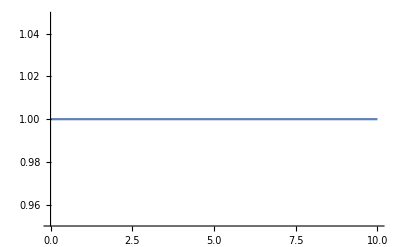

```mathematica
Plot[Conjugate[a]/b,{κ,0,10}]
```

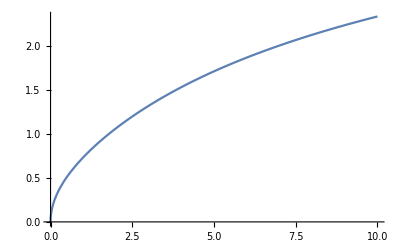

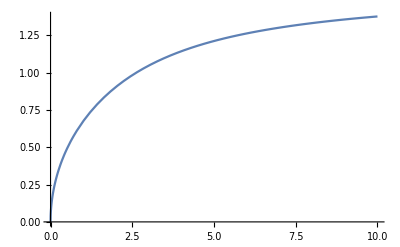

-Graphics3D-

-Graphics3D-

```mathematica
Plot[Re[Log[a]],{κ,0,10}]
Plot[Im[Log[a]],{κ,0,10}]
Plot3D[Re[-ⅈ/(2 π^2 λ)(Exp[m x]ArcTan[√((α-2 Cosh[x])/(β+2 Cosh[x]))])],{x,0,10},{κ,0,10}]
Plot3D[Im[-ⅈ/(2 π^2 λ)(Exp[m x]ArcTan[√((α-2 Cosh[x])/(β+2 Cosh[x]))])],{x,0,10},{κ,0,10}]
```

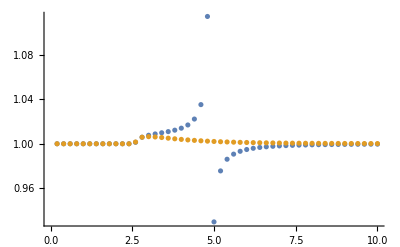

```mathematica
Clear[y]
tmp1=Table[{κ,Re[NIntegrate[-ⅈ/(2 π^2 λ)(Exp[m x]ArcTan[√((α-2 Cosh[x])/(β+2 Cosh[x]))]),{x,-Log[a],Log[a]}]]/Re[NIntegrate[-ⅈ/(2 π^2 λ)((y^(-1+m) (-1+y^2))/(2 m (1+y^2+y (2-ⅈ κ)) √(-(1-2 y+y^2-ⅈ y κ)/(1+2 y+y^2-ⅈ y κ)))),{y,1/a,a}]]},{κ,0.2,10,0.2}]//Quiet;
tmp2=Table[{κ,Im[NIntegrate[-ⅈ/(2 π^2 λ)(Exp[m x]ArcTan[√((α-2 Cosh[x])/(β+2 Cosh[x]))]),{x,-Log[a],Log[a]}]]/Im[NIntegrate[-ⅈ/(2 π^2 λ)((y^(-1+m) (-1+y^2))/(2 m (1+y^2+y (2-ⅈ κ)) √(-(1-2 y+y^2-ⅈ y κ)/(1+2 y+y^2-ⅈ y κ)))),{y,1/a,a}]]},{κ,0.2,10,0.2}]//Quiet;

ListPlot[{tmp1,tmp2},PlotRange->Full]
Clear[y,κ]
```

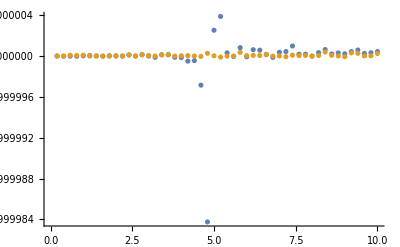

```mathematica
y=1/a(1-t)+a t;
tmp3=Table[{κ,Re[NIntegrate[-ⅈ/(2 π^2 λ)(Exp[m x]ArcTan[√((α-2 Cosh[x])/(β+2 Cosh[x]))]),{x,-Log[a],Log[a]}]]/Re[NIntegrate[-ⅈ/(2 π^2 λ)((y^(-1+m) (-1+y^2))/(-2 m Sign[Re[(1+y^2+y (2-ⅈ κ))]]Sign[Im[(1+y^2+y (2-ⅈ κ)) (1-2 y+y^2-ⅈ y κ)]] √(-(1+y^2+y (2-ⅈ κ)) (1-2 y+y^2-ⅈ y κ)))),{y,1/a,a}]]},{κ,0.2,10,0.2}]//Quiet;
tmp4=Table[{κ,Im[NIntegrate[-ⅈ/(2 π^2 λ)(Exp[m x]ArcTan[√((α-2 Cosh[x])/(β+2 Cosh[x]))]),{x,-Log[a],Log[a]}]]/Im[NIntegrate[-ⅈ/(2 π^2 λ)((y^(-1+m) (-1+y^2))/(-2 m Sign[Re[(1+y^2+y (2-ⅈ κ))]]Sign[Im[(1+y^2+y (2-ⅈ κ)) (1-2 y+y^2-ⅈ y κ)]] √(-(1+y^2+y (2-ⅈ κ)) (1-2 y+y^2-ⅈ y κ)))),{y,1/a,a}]]},{κ,0.2,10,0.2}]//Quiet;

ListPlot[{tmp3,tmp4},PlotRange->Full]
Clear[y,κ]
```

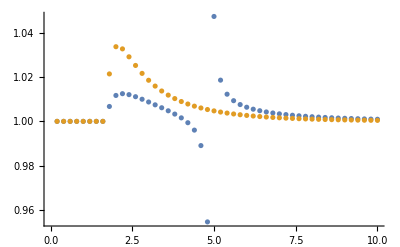

```mathematica
y=1/a(1-t)+a t;

tmp5=Table[{κ,Re[NIntegrate[-ⅈ/(2 π^2 λ)(Exp[m x]ArcTan[√((α-2 Cosh[x])/(β+2 Cosh[x]))]),{x,-Log[a],Log[a]}]]/Re[NIntegrate[-ⅈ/(2 π^2 λ)(√(-κ (-4 ⅈ+κ))(y^(-1+m) (-1+y^2))/(-2 m Sign[4+√κ (-(-1+t) t κ^(3/2)-√2 √(κ (-κ+√(16+κ^2)))+2 √2 t √(κ (-κ+√(16+κ^2))))]Sign[- (-1+t) t κ (-16+(-1+2 t) √κ ((-2+4 t) κ^(3/2)-4 √2 √(-κ+√(16+κ^2))+√2 κ √(κ+√(16+κ^2))))] √(-(1+y^2+y (2-ⅈ κ)) (1-2 y+y^2-ⅈ y κ)))),{t,0,1}]]},{κ,0.2,10,0.2}]//Quiet;
tmp6=Table[{κ,Im[NIntegrate[-ⅈ/(2 π^2 λ)(Exp[m x]ArcTan[√((α-2 Cosh[x])/(β+2 Cosh[x]))]),{x,-Log[a],Log[a]}]]/Im[NIntegrate[-ⅈ/(2 π^2 λ)(√(-κ (-4 ⅈ+κ))(y^(-1+m) (-1+y^2))/(-2 m Sign[4+√κ (-(-1+t) t κ^(3/2)-√2 √(κ (-κ+√(16+κ^2)))+2 √2 t √(κ (-κ+√(16+κ^2))))]Sign[- (-1+t) t κ (-16+(-1+2 t) √κ ((-2+4 t) κ^(3/2)-4 √2 √(-κ+√(16+κ^2))+√2 κ √(κ+√(16+κ^2))))] √(-(1+y^2+y (2-ⅈ κ)) (1-2 y+y^2-ⅈ y κ)))),{t,0,1}]]},{κ,0.2,10,0.2}]//Quiet;

ListPlot[{tmp5,tmp6},PlotRange->Full]
Clear[y,κ]
```

```mathematica
y=1/a(1-t)+a t;

tmp7=Table[{κ,Re[NIntegrate[-ⅈ/(2 π^2 λ)(Exp[m x]ArcTan[√((α-2 Cosh[x])/(β+2 Cosh[x]))]),{x,-Log[a],Log[a]}]]/Re[NIntegrate[-ⅈ/(2 π^2 λ)(√(-κ (-4 ⅈ+κ))(y^(-1+m) (-1+y^2))/(-2 m √(-(1+y^2+y (2-ⅈ κ)) (1-2 y+y^2-ⅈ y κ))))If[t>1/2+(√2 √(κ (-κ+√(16+κ^2))))/κ^(3/2)-(√(κ^2 ((-8+κ) κ+8 (2+√(16+κ^2)))))/(2 κ^2) && t<1/(8 κ^2)(4 κ^2+4 √2 √κ √(-κ+√(16+κ^2))-√2 κ^(3/2) √(κ+√(16+κ^2))+√2 √(κ (16 √(16+κ^2)+κ (48-8 √(-κ+√(16+κ^2)) √(κ+√(16+κ^2))+κ (κ+√(16+κ^2)))))),-1,1],{t,0,1}]]},{κ,0.2,10,0.2}]//Quiet;

tmp8=Table[{κ,Im[NIntegrate[-ⅈ/(2 π^2 λ)(Exp[m x]ArcTan[√((α-2 Cosh[x])/(β+2 Cosh[x]))]),{x,-Log[a],Log[a]}]]/Im[NIntegrate[-ⅈ/(2 π^2 λ)(√(-κ (-4 ⅈ+κ))(y^(-1+m) (-1+y^2))/(-2 m √(-(1+y^2+y (2-ⅈ κ)) (1-2 y+y^2-ⅈ y κ))))If[t>(κ+2 √2 √(-κ+√(16+κ^2))-√((-8+κ) κ+8 (2+√(16+κ^2))))/(2 κ) && t<1/(8 κ^(3/2))(4 κ^(3/2)+4 √2 √(-κ+√(16+κ^2))-√2 κ √(κ+√(16+κ^2))+√(32 √(16+κ^2)+2 κ (48-8 √(-κ+√(16+κ^2)) √(κ+√(16+κ^2))+κ (κ+√(16+κ^2))))),-1,1],{t,0,1}]]},{κ,0.2,10,0.2}]//Quiet;


ListPlot[{tmp7,tmp8},PlotRange->Full]
Clear[y,κ]
```

-Graphics-

## Steps towards expressions above

```mathematica
((1+y^2+y (2-ⅈ κ))/.y->1/a(1-t)+a t//FullSimplify)/.{√(-κ (-4 ⅈ+κ))->√κ(√((κ √(κ^2+16)-κ^2)/2)+ⅈ √((κ √(κ^2+16)+κ^2)/2))}//Expand//Collect[#,ⅈ]&

((1+y^2+y (2-ⅈ κ)) (1-2 y+y^2-ⅈ y κ)/.y->1/a(1-t)+a t//FullSimplify)/.{√(-κ (-4 ⅈ+κ))->((√κ (√(-κ+√(16+κ^2))+ⅈ √(κ+√(16+κ^2))))/(√2))}//Expand//Collect[#,ⅈ]&
```

4+2 ⅈ κ-4 ⅈ t κ+4 ⅈ t^2 κ+t κ^2-t^2 κ^2-√2 √κ √(-κ^2+κ √(16+κ^2))+2 √2 t √κ √(-κ^2+κ √(16+κ^2))-ⅈ √2 √κ √(κ^2+κ √(16+κ^2))+2 ⅈ √2 t √κ √(κ^2+κ √(16+κ^2))

-16 ⅈ t κ+16 ⅈ t^2 κ+12 t κ^2-28 t^2 κ^2+32 t^3 κ^2-16 t^4 κ^2+2 ⅈ t κ^3-10 ⅈ t^2 κ^3+16 ⅈ t^3 κ^3-8 ⅈ t^4 κ^3+t^2 κ^4-2 t^3 κ^4+t^4 κ^4+4 ⅈ √2 t κ^(3/2) √(-κ+√(16+κ^2))-12 ⅈ √2 t^2 κ^(3/2) √(-κ+√(16+κ^2))+8 ⅈ √2 t^3 κ^(3/2) √(-κ+√(16+κ^2))-√2 t κ^(5/2) √(-κ+√(16+κ^2))+3 √2 t^2 κ^(5/2) √(-κ+√(16+κ^2))-2 √2 t^3 κ^(5/2) √(-κ+√(16+κ^2))-4 √2 t κ^(3/2) √(κ+√(16+κ^2))+12 √2 t^2 κ^(3/2) √(κ+√(16+κ^2))-8 √2 t^3 κ^(3/2) √(κ+√(16+κ^2))-ⅈ √2 t κ^(5/2) √(κ+√(16+κ^2))+3 ⅈ √2 t^2 κ^(5/2) √(κ+√(16+κ^2))-2 ⅈ √2 t^3 κ^(5/2) √(κ+√(16+κ^2))

{{t→1/2+(√2 √(κ (-κ+√(16+κ^2))))/κ^(3/2)-(√(κ^2 ((-8+κ) κ+8 (2+√(16+κ^2)))))/(2 κ^2)},{t→(κ^2+2 √2 √κ √(κ (-κ+√(16+κ^2)))+√(κ^2 ((-8+κ) κ+8 (2+√(16+κ^2)))))/(2 κ^2)}}

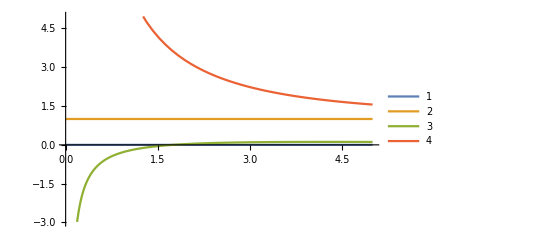

{{κ→1/4+1/(4 √(3/(3-(32 6^(2/3))/(-9+√3153)^(1/3)+4 (6 (-9+√3153))^(1/3))))+1/2 √(1/2-(2 (-9+√3153))^(1/3)/3^(2/3)+(8 2^(2/3))/(3 (-9+√3153))^(1/3)+1/2 √(3/(3-(32 6^(2/3))/(-9+√3153)^(1/3)+4 (6 (-9+√3153))^(1/3))))}}

{{κ→1.7484}}

```mathematica
Solve[4+√κ (-(-1+t) t κ^(3/2)-√2 √(κ (-κ+√(16+κ^2)))+2 √2 t √(κ (-κ+√(16+κ^2))))==0,t]//FullSimplify
Plot[{0,1,1/2+(√2 √(κ (-κ+√(16+κ^2))))/κ^(3/2)-(√(κ^2 ((-8+κ) κ+8 (2+√(16+κ^2)))))/(2 κ^2),(κ^2+2 √2 √κ √(κ (-κ+√(16+κ^2)))+√(κ^2 ((-8+κ) κ+8 (2+√(16+κ^2)))))/(2 κ^2)},{κ,0,5},PlotLegends->{"1","2","3","4"}]
Solve[1/2+(√2 √(κ (-κ+√(16+κ^2))))/κ^(3/2)-(√(κ^2 ((-8+κ) κ+8 (2+√(16+κ^2)))))/(2 κ^2)==0,κ]//Simplify
%//N
```

{{t→0},{t→1},{t→-1/(8 κ^2)(-4 κ^2-4 √2 √κ √(-κ+√(16+κ^2))+√2 κ^(3/2) √(κ+√(16+κ^2))+√2 √(κ (16 √(16+κ^2)+κ (48-8 √(-κ+√(16+κ^2)) √(κ+√(16+κ^2))+κ (κ+√(16+κ^2))))))},{t→1/(8 κ^2)(4 κ^2+4 √2 √κ √(-κ+√(16+κ^2))-√2 κ^(3/2) √(κ+√(16+κ^2))+√2 √(κ (16 √(16+κ^2)+κ (48-8 √(-κ+√(16+κ^2)) √(κ+√(16+κ^2))+κ (κ+√(16+κ^2))))))}}

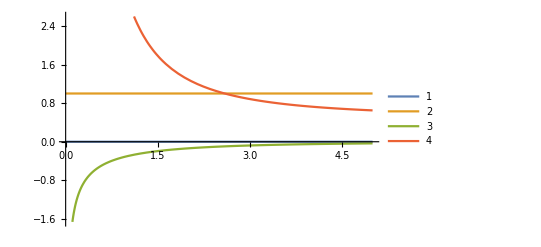

{{κ→2/3 (2-(4 2^(2/3))/(13+3 √33)^(1/3)+(26+6 √33)^(1/3))}}

{{κ→2.5912}}

```mathematica
Solve[- (-1+t) t κ (-16+(-1+2 t) √κ ((-2+4 t) κ^(3/2)-4 √2 √(-κ+√(16+κ^2))+√2 κ √(κ+√(16+κ^2))))==0,t]//FullSimplify
Plot[{0,1,-1/(8 κ^2)(-4 κ^2-4 √2 √κ √(-κ+√(16+κ^2))+√2 κ^(3/2) √(κ+√(16+κ^2))+√2 √(κ (16 √(16+κ^2)+κ (48-8 √(-κ+√(16+κ^2)) √(κ+√(16+κ^2))+κ (κ+√(16+κ^2)))))),1/(8 κ^2)(4 κ^2+4 √2 √κ √(-κ+√(16+κ^2))-√2 κ^(3/2) √(κ+√(16+κ^2))+√2 √(κ (16 √(16+κ^2)+κ (48-8 √(-κ+√(16+κ^2)) √(κ+√(16+κ^2))+κ (κ+√(16+κ^2))))))},{κ,0,5},PlotLegends->{"1","2","3","4"}]
Solve[1/(8 κ^2)(4 κ^2+4 √2 √κ √(-κ+√(16+κ^2))-√2 κ^(3/2) √(κ+√(16+κ^2))+√2 √(κ (16 √(16+κ^2)+κ (48-8 √(-κ+√(16+κ^2)) √(κ+√(16+κ^2))+κ (κ+√(16+κ^2))))))==1,κ]//Simplify
%//N
```